```mathematica
*Hankel_Function_Type_1*
```

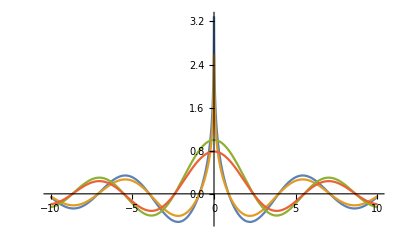

```mathematica
A1[k_]:=NIntegrate[Exp[Abs[k]*Sinh[x]],{x,-200,0}]
A2[k_]:=NIntegrate[Exp[-Abs[k]*Sinh[x]],{x,0,200}]
A3[k_]:=NIntegrate[ⅈ*Exp[ⅈ*Abs[k]*Sin[x]],{x,0,π}]
Cal[k_]:=A1[k]+A2[k]+A3[k]
Plot[{Im[HankelH2[0,Abs[k]]],Im[(-ⅈ/4)*Cal[k]],Re[HankelH2[0,Abs[k]]],Re[(-ⅈ/4)*Cal[k]]},{k,-10,10},PlotRange->Full]
```

```mathematica
*Hankel_Function_Type_2*
```

```mathematica
A1[k_]:=NIntegrate[Exp[Abs[k]*Sinh[x]],{x,-200,0}]
A2[k_]:=NIntegrate[Exp[-Abs[k]*Sinh[x]],{x,0,200}]
A3[k_]:=NIntegrate[-ⅈ*Exp[-ⅈ*Abs[k]*Sin[x]],{x,0,π}]
Cal[k_]:=A1[k]+A2[k]+A3[k]
Plot[{Im[HankelH2[0,Abs[k]]],Im[(ⅈ/4)*Cal[k]],Re[HankelH2[0,Abs[k]]],Re[(ⅈ/4)*Cal[k]]},{k,-10,10},PlotRange->Full]
```

-Graphics-